# Homework 7

Shahaf zohar - 205978000
 Roey salah - 206115438

Play around with "Network of Thrones" . Compare the tribe to community detecting
algorithms . What is working best .

Using Mathematica FindGraphCommunities function . What is working the best?

Using “Edge Betweenness Algorithm” (and Hierarchical Clustering) . Does it finds a it finds a “good”  dendrogram tree?Explain/show .

Using Hierarchical Clustering and a similarity measure Does it finds a “good” dendrogram
tree?Explain/show .

Using the “Louvain Modularity” method (need to implement it) .

Bounus : Playaround with the Facebook network : Find something intresting (you can use all previous units) .

#### Loading The Network

{Aegon,Aemon,Aerys,Alliser,Amory,Anguy,Arya,Balon,Barristan,Belwas,Beric,Bowen,Bran,Brienne,Bronn,Brynden,Catelyn,Cersei,Chataya,Craster,Cressen,Daario,Daenerys,Dalla,Davos,Doran,Drogo,Eddard,Eddison,Edmure,Elia,Ellaria,Gendry,Gilly,Gregor,Grenn,Hodor,Hoster,Illyrio,Ilyn,Irri,Jaime,Janos,Jeyne,Joffrey,Jojen,Jon,Jon Arryn,Jorah,Karl,Kevan,Kraznys,Lancel,Loras,Lothar,Luwin,Lysa,Mace,Mance,Margaery,Marillion,Meera,Melisandre,Meryn,Missandei,Myrcella,Nan,Oberyn,Olenna,Orell,Petyr,Podrick,Pycelle,Qhorin,Qyburn,Rakharo,Ramsay,Rattleshirt,Renly,Rhaegar,Rickard,Rickon,Robb,Robert,Robert Arryn,Roose,Roslin,Salladhor,Samwell,Sandor,Sansa,Shae,Shireen,Stannis,Styr,Theon,Thoros,Tommen,Tyrion,Tywin,Val,Varys,Viserys,Walder,Walton,Worm,Ygritte}

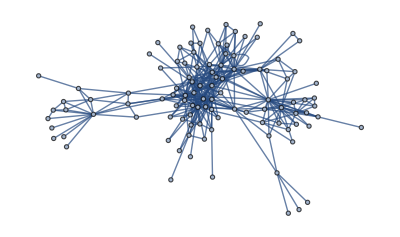

```mathematica
SetDirectory[NotebookDirectory[]];
file=Rest[Import["stormofswords.csv"]];
tribes=Import["tribes.csv"];
nodes=Flatten[tribes⟦All,1⟧]
nodesTribe=Flatten[tribes[[All,2]]];
edges=#⟦1⟧<->#⟦2⟧&/@file[[All,{1,2}]];
G=Graph[nodes,edges]
```

#### Functions from the class

```mathematica
Needs["HierarchicalClustering`"];
Off[DirectAgglomerate::ties];
BetweennessCut[g_]:= Module[{graph=g},
While[Length[cc=ConnectedComponents[graph]]<2,
graph= EdgeDelete[graph,TopEdgeBetweennessCentrality[graph]];];
cc]
TopEdgeBetweennessCentrality[g_]:=EdgeList[g][[Ordering[EdgeBetweennessCentrality[g],-1]]]
NextBetweennessEdge[g_,i_]:=Module[{graph=g,list={}},
For[j=1,j≤i,j++,
list=Union[list,TopEdgeBetweennessCentrality[graph]];
graph= EdgeDelete[graph,TopEdgeBetweennessCentrality[graph]];];
list]
BetweennessClusters[g_]:=Module[{graph=g,list={},c,d,e},
If[VertexCount[g]==1,First@VertexList[g],c=BetweennessCut[g];
Cluster[BetweennessClusters[d=Subgraph[g,First@c]],BetweennessClusters[e=Subgraph[g,Last@c]],EdgeCount[g],Length[First@c],Length[Last@c]]]]
CosineDistanceMatrix[A_]:=
Table[Table[CosineDistance[Normal[A[[i]]],Normal[A[[j]]]],{i,1,Length[A]}],{j,1,Length[A]}]
```

#### Task 1

The Thread function is used to create a list of rules that map each vertex to its corresponding "Tribe" value . the value of the "Tribe" property for the vertex "Salladhor" . 
	The result is stored in the variable Temp .

```mathematica
(*add the Tribe property*)
G=SetProperty[{G,VertexList[G]},Thread["Tribe"->nodesTribe]];
Temp=PropertyValue[{G,"Salladhor"},"Tribe"]
```

6

```mathematica
(*Pratuition each tribe dependent on Vertex in G*)
VertexConference=PropertyValue[{G,#},"Tribe"]&/@VertexList[G];
X=Tally[VertexConference]
Length[X]
```

{{5,15},{1,19},{4,40},{7,7},{2,8},{3,12},{6,6}}

7

```mathematica
(*Pratuition each tribe dependent on Communities in G*)
meanValues=PropertyValue[{G,#},"Tribe"]&/@FindGraphCommunities[G]
Length[meanValues]
```

{{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,7,4,4,4,4,4,4},{1,1,1,1,6,1,6,1,1,1,2,1,2,1,1,1,2,6,1,1,1,6,1,6,6,1,1,1},{7,2,4,3,3,4,7,3,3,3,3,2,4,4,2,4,3,3,2,3,4,3,3,4,2,3},{5,5,5,5,5,5,5,5,4,5,5,5,5,5,4,5,5},{7,7,7,7}}

5

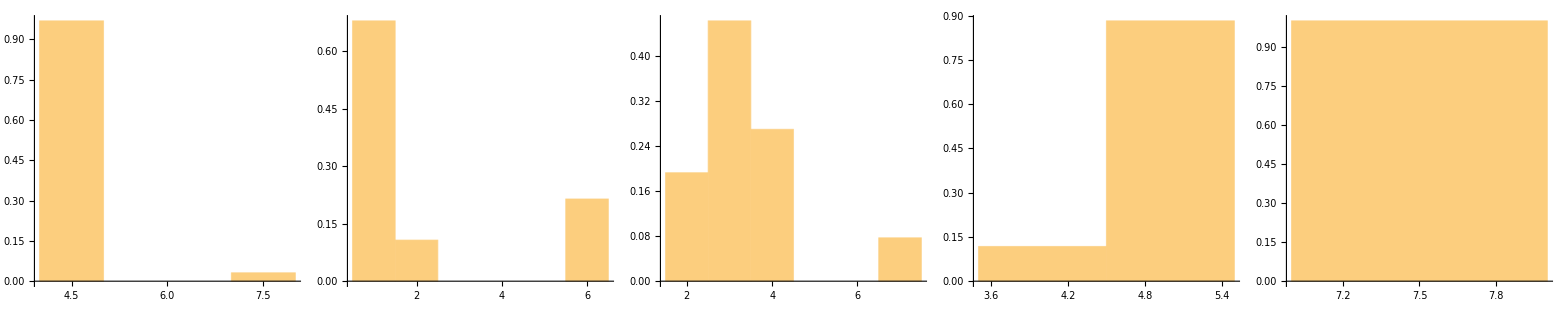

```mathematica
Conference=DeleteDuplicates[meanValues];
histograms=Histogram[#,{1},"PDF"]&/@Conference;
Grid[Partition[histograms,Length[ls]]]
```

Summary and explanation

The best division is by communities as shown, After attempts to find the best partition of that graph
    This code calculates the mean tribe value of each vertex in a graph G .
  	1.FindGraphCommunities is used to obtain the communities of the graph .
  	2. For each vertex in G, the PropertyValue function is used to get the tribe value, and the mean value is calculated for each community .
  	3. The DeleteDuplicates function is used to remove the duplicate values ​​of meanValues . The Histogram function is used to create a histogram 
  	for each unique tribe value in meanValues ​​with bin size 1 and normalized to "PDF" .
  	4. The Grid function is used to display the histograms in a grid format with the number of columns equal to the length of the Conference list .

### Task 2

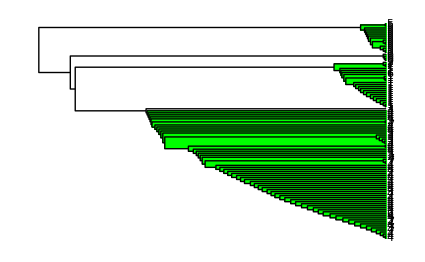

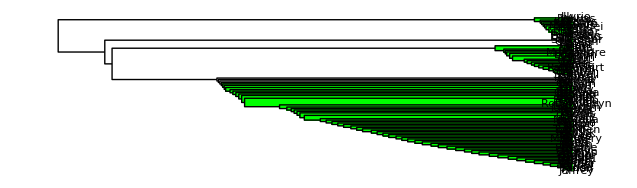

```mathematica
BetweennessG=BetweennessClusters[G];
DendrogramPlot[BetweennessG,Orientation->Left,LeafLabels->(PropertyValue[{G,#},"Tribe"]&),BaseStyle->{FontSize->5},HighlightLevel->5]
Show[Graphics[Disk[{3,15},1.5]],DendrogramPlot[BetweennessG,Orientation->Left,LeafLabels->(#&),HighlightLevel->7]]
```

### Task 3 Hierarchical clustering

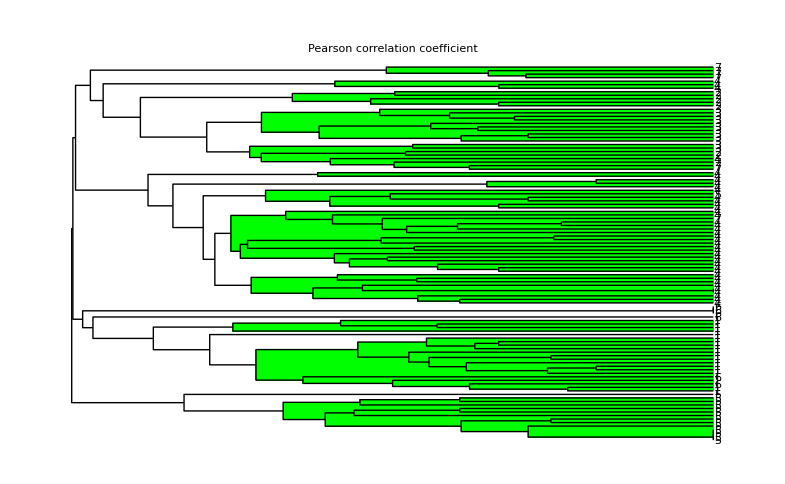

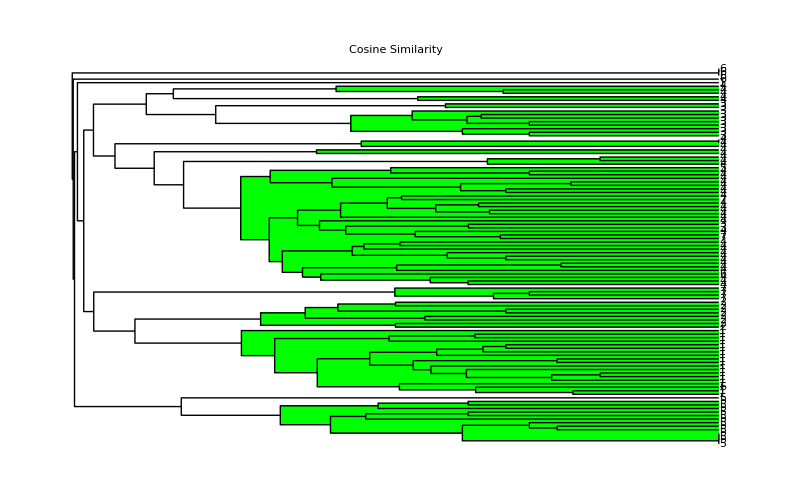

```mathematica
A=AdjacencyMatrix[G];
DendrogramPlot[DirectAgglomerate[-(Correlation[A]-1),VertexList[G],Linkage->"Average"],LeafLabels->(PropertyValue[{G,#},"Tribe"]&),Orientation->Left,BaseStyle->{FontSize->5},HighlightLevel->7,PlotLabel->"Pearson correlation coefficient"]
DendrogramPlot[DirectAgglomerate[CosineDistanceMatrix[A],VertexList[G],Linkage->"Average"],LeafLabels->(PropertyValue[{G,#},"Tribe"]&),Orientation->Left,HighlightLevel->7,BaseStyle->{FontSize->5},PlotLabel->"Cosine Similarity "]
```

Summary and explanation

These commands are creating two dendrogram plots that show the hierarchical clustering of the nodes in a graph based on their similarity . 		
	The first dendrogram plot uses the Pearson correlation coefficient as a similarity measure between the nodes, and the second dendrogram 
	plot uses the cosine similarity measure .

### Similarity

Cosine similarity measures the similarity between two vectors of an inner product space . It is measured by the cosine of the angle between two vectors and determines whether two vectors are pointing in roughly the same direction . It is often used to measure document similarity in text analysis

```mathematica
Manipulate[Column[{HighlightGraph[G,{VertexList[G]⟦i=First@First@Position[VertexList[G],x]⟧,VertexList[G]⟦j=First@First@Position[VertexList[G],y]⟧}],Normal[A⟦i⟧],Normal[A⟦j⟧],"Perason Correlation: "<>ToString[N[-(Correlation[A⟦i⟧,A⟦j⟧]-1),4]],"Cosine Similarity: "<>ToString[N[CosineDistance[Normal[A⟦i⟧],Normal[A⟦j⟧]],4]]}],{x,VertexList[G]},{y,VertexList[G]}]
```

### Task 4

### Modularity method

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

{{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{1,1,1,1,6,1,6,1,1,1,1,1,1,1,6,1,1,1,6,1,6,6,1,1,1},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{7,7,7,7,7,4,7,7},{2,2,2,2,2,2,2,2},{4,3,3,3,3,3,4,3,4,4,4,4,3,3,3,4,3,3,4,3}}

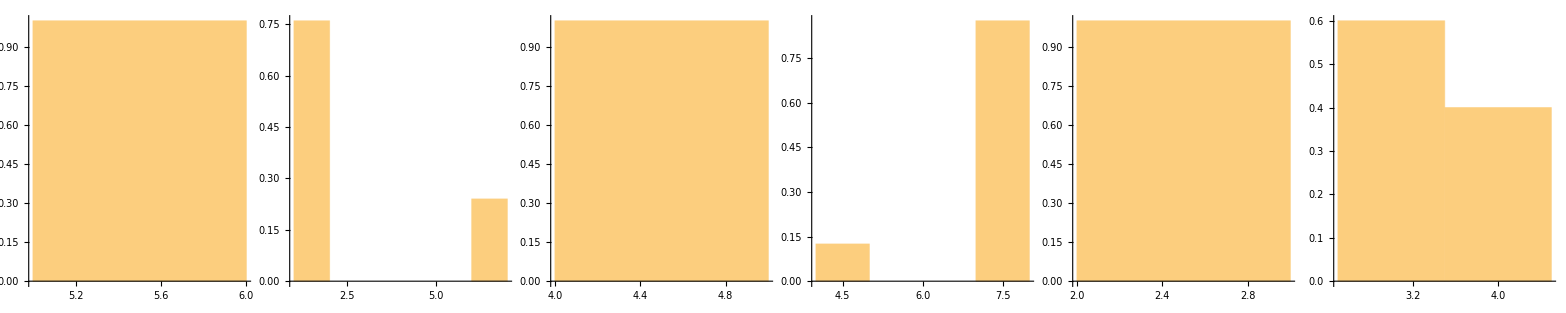

-Graphics-

```mathematica
cl=IGCommunitiesMultilevel[G];
clcl=cl["Communities"];
meanTribeValues=PropertyValue[{G,#},"Tribe"]&/@clcl
histograms=Histogram[#,{1},"PDF"]&/@meanTribeValues;
Grid[Partition[histograms,Length[clcl]]]
CommunityGraphPlot[G,clcl]
```

Summary and explanation

In general, the code is performing community detection analysis on the graph G . It first uses the IGCommunitiesMultilevel function to identify the different communities in G . 
	The code then calculates the mean tribe values for each community and creates a histogram for each community . Finally, it plots the graph with each community colored differently using the CommunityGraphPlot function .
	We had to download the IGraphM folder to implement this task